Generating data for m0 = 0

Generating data for m0 = 1

Generating data for m0 = 2

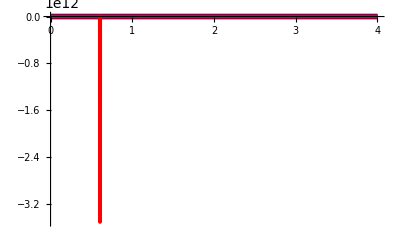

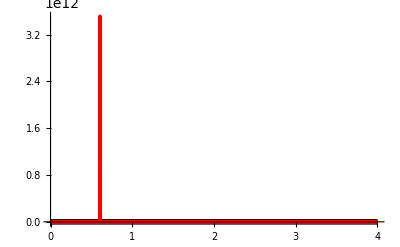

```mathematica
(* Recursive construction of expansion coefficients *)
σ1=-1; σ2=+1; σ3=1;
(* Lattice kinematics *)
LS=2;
mD[p_]:=4 Sin[1/2(2π p)/LS]^2;
(*MeanLink[λ_]:=If[λ<4,1-λ/8,2/λ];*)
MeanLink[λ_]:=2/λ;
m2[λ_]:=σ2/σ3(2 (1-MeanLink[λ])-σ1 λ);
G0[λ_,p_]:=1/(m2[λ]+mD[p]);
DeltaP[p_]:=If[Mod[p,LS]==0,1,0];
(* n is the number of momenta in the correlator *)
(* m is the order in the formal λ - expansion *)
(* P is the 2 n - sized list of momenta *)
G[λ_,P_,m_]:=Module[{n,Res0,Res1,Res2,Res3,A,p1t,p2t,q1t,pAt,qAt,m1,m2,P1,P2,i},
Res1=0; Res2=0; Res3=0;
n=Length[P]/2;
If[m==0,
(* We're at the bottom of the recursion - just the free propagator *)
Res0=Product[1/LS DeltaP[ P[[2 i - 1]]+P[[2 i]] ] G0[λ,P[[2i-1]]] ,{i,1,n}];
,
(* Else - go to lower levels by using the SD equations *)
(* First term in the SD equation *)
Res0=If[n>1,1/LS G0[λ,P[[1]]] DeltaP[P[[1]]+P[[2]]] G[λ,Drop[P,2],m], 0];
(* Second term in the SD equation - switch momenta *)
For[A=2,A≤n,A++,
P1=Take[P,2(A-1)]; 
P2=Drop[P,2(A-1)];
For[p1t=0,p1t<LS,p1t++,
pAt=P[[1]]+P[[2A-1]]-p1t;
P1[[1]]=p1t; P2[[1]]=pAt;
For[m1=0,m1<m,m1++,
m2=m-m1-1;
Res1+=σ2/σ3 1/LS G[λ,P1,m1] G[λ,P2,m2] ;
];
];
];
(* Third term in SD equations - join sequences with vertex *)
For[A=2,A≤n,A++,
P1=Take[P,2A]; 
P2=Drop[P,2(A-1)];
For[p1t=0,p1t<LS,p1t++,
For[pAt=0,pAt<LS,pAt++,
qAt=P[[1]]-p1t-pAt;
P1[[1]]=p1t;P1[[2A]]=qAt;P2[[1]]=pAt;
For[m1=0,m1<m,m1++,
m2=m-m1-1;
Res2+=-σ2/σ3 mD[qAt] G[λ,P1,m1] G[λ,P2,m2] ;
];
];
];
];
(* Fourth term in SD equations - create vertex *)
For[p1t=0,p1t<LS,p1t++,
For[p2t=0,p2t<LS,p2t++,
q1t=P[[1]]-p1t -p2t;
P1=P;
P1[[1]]=p2t;
PrependTo[P1,q1t];
PrependTo[P1,p1t];
Res3 +=-(σ1 σ2)/σ3 mD[q1t] G[λ,P1,m-1];
];
];
];
(* Final operation *)
Res0 + (Res1 + Res2+ Res3) G0[λ,P[[1]]]
];
mmax=2; λmin=0.0; λmax=4.0;
USum=Table[0,{m0,0,mmax}]; LSum=Table[0,{m0,0,mmax}];
mUSum=0; mLSum = 0;
GrU={Plot[1,{λ,λmin,λmax},PlotStyle->{Thickness[0.01],Black},PlotRange->All]};
GrL={Plot[If[λ<4,1-λ/8,2/λ],{λ,λmin,λmax},PlotStyle->{Thickness[0.01],Black},PlotRange->All]};
For[m0=0,m0≤mmax,m0++,
Print["Generating data for m0 = ",m0];
r=m0/mmax;
G00=FullSimplify[λ^(m0+1) G[λ,{0,0},m0]];
G11=FullSimplify[λ^(m0+1) G[λ,{1,1},m0]];
mUSum += (G00 + G11);
mLSum += (G00 - G11);
USum[[m0+1]]=mUSum;
LSum[[m0+1]]=mLSum;
AppendTo[GrU,Plot[mUSum,{λ,λmin,λmax},PlotStyle->{Thickness[0.007],RGBColor[r,0,1-r]},PlotRange->All]];AppendTo[GrL,Plot[mLSum,{λ,λmin,λmax},PlotStyle->{Thickness[0.007],RGBColor[r,0,1-r]},PlotRange->All]];
];
Print[Show[GrU,PlotRange->All]];
Print[Show[GrL,PlotRange->All]];
```

```mathematica
λ0=0.1;
N[m2[λ]/.{λ->λ0}]
For[m=1,m≤mmax+1,m++,
sU=N[USum[[m]]/.{λ->λ0}];
sL=N[LSum[[m]]/.{λ->λ0}];
Print[sU," ",sL];
];
Print[USum[[2]],", ",LSum[[2]]]
```

-37.9

-0.00279419 0.000155665

-0.00279465 0.000155716

-0.00279465 0.000155716

λ^2/(2 (-4+λ (2+λ)))+λ^5/(-4+λ (6+λ))^3+λ^2/(2 (-4+λ (6+λ)))+λ^5/((-4+λ (2+λ))^2 (-4+λ (6+λ))), λ^2/(2 (-4+λ (2+λ)))-λ^5/(-4+λ (6+λ))^3-λ^2/(2 (-4+λ (6+λ)))+λ^5/((-4+λ (2+λ))^2 (-4+λ (6+λ)))

```mathematica
(* Some testing for the m=1 fourth-order correlator *)
λ0=2.0;
G41=Table[{{p1,p2,p3,p4},G[λ0,{p1,p2,p3,p4},2]},{p1,0,1,1},{p2,0,1,1},{p3,0,1,1},{p4,0,1,1}];
G41=Flatten[G41,3];
For[i=1,i≤Length[G41],i++,
SC=Mod[Total[G41[[i,1]]],2];
If[SC==0,
Print[G41[[i]]];
];
];
```

{{0,0,0,0},0.00675248}

{{0,0,1,1},0.00110783}

{{0,1,0,1},0.000257694}

{{0,1,1,0},0.000347327}

{{1,0,0,1},0.000347327}

{{1,0,1,0},0.000257694}

{{1,1,0,0},0.00110783}

{{1,1,1,1},0.000206513}

```mathematica
2.825671 10^-3
```

```mathematica
0.002825671/0.0013108784706417846
```

2.15556

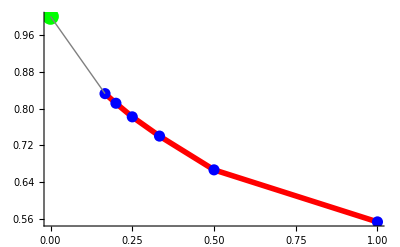

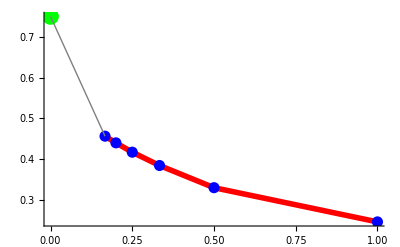

```mathematica
ExtrapolationPlot[App_,λ0_,ExRes_]:=Module[{TD,i,Gr1,Gr2},
TD=Table[{1/i,App[[i]]/.{λ->λ0}},{i,1,Length[App]}];
Gr1=ListPlot[TD,Joined->True,PlotStyle->{Thickness[0.01],Red},PlotRange->{{-0.05,1.0},{0.0,1.1}}];
Gr2=ListPlot[TD,Joined->False,PlotStyle->{PointSize[0.02],Blue}];
Gr3=Graphics[{PointSize[0.03],Green,Point[{0.0,ExRes}],Gray,Line[{{0.0,ExRes},TD[[Length[TD]]]} ]}];
Print[Show[Gr1,Gr2,Gr3,PlotRange->All]];
];
λ0=2.0;
ExtrapolationPlot[USum,λ0,1.0];
ExtrapolationPlot[LSum,λ0,1.0-λ0/8];
```

```mathematica
N[0.2 0.02461538]
```

0.00492308

```mathematica
8 2^24/(1024 1024)
```

128

```mathematica
2^24
```

16777216

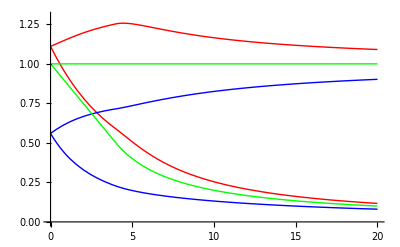

```mathematica
U1pm[λ_]:=If[λ<4,2/3+λ^2/(4+(3 λ)/4)^3+(2 λ)/(16+3 λ)+64/(144+27 λ),λ^2/(8-4 λ+2 λ^2)+λ^2/(8+4 λ+2 λ^2)+λ^5/(4+λ (2+λ))^3+λ^5/((4+(-2+λ) λ)^2 (4+λ (2+λ)))];
L1pm[λ_]:=If[λ<4,2/3-λ^2/(4+(3 λ)/4)^3-(2 λ)/(16+3 λ)+64/(144+27 λ),λ^2/(8-4 λ+2 λ^2)-λ^2/(8+4 λ+2 λ^2)-λ^5/(4+λ (2+λ))^3+λ^5/((4+(-2+λ) λ)^2 (4+λ (2+λ)))];
U1mp[λ_]:=If[λ<4,2/5+λ^2/(4+(5 λ)/4)^3+(2 λ)/(16+5 λ)+64/(400+125 λ),λ^2/(2 (-4+λ (2+λ)))+λ^5/(-4+λ (6+λ))^3+λ^2/(2 (-4+λ (6+λ)))+λ^5/((-4+λ (2+λ))^2 (-4+λ (6+λ)))];
L1mp[λ_]:=If[λ<4,2/5-λ^2/(4+(5 λ)/4)^3-(2 λ)/(16+5 λ)+64/(400+125 λ),λ^2/(2 (-4+λ (2+λ)))-λ^5/(-4+λ (6+λ))^3-λ^2/(2 (-4+λ (6+λ)))+λ^5/((-4+λ (2+λ))^2 (-4+λ (6+λ)))];
Plot[{U1pm[λ],L1pm[λ],U1mp[λ],L1mp[λ],If[λ<4,1-λ/8,2/λ],1},{λ,0,20},PlotRange->{0.0,1.3},PlotStyle->{Red,Red,Blue,Blue,Green,Green}]
```